```mathematica
$Assumptions = {Vg ∈ Reals, V0 ∈ Reals, κ ∈ Reals, a ∈ Reals, n ∈ Integers, Subscript[k, F] ∈ Reals, q ∈ Reals, q > 0}
```

{Vg∈ℝ,V0∈ℝ,κ∈ℝ,a∈ℝ,n∈ℤ,k_F∈ℝ,q∈ℝ,q>0}

```mathematica
d1H = FullSimplify[(Vg/3)(1/(8 π (1+κ^2)^2)(8 π (1+κ^2)-4 q π κ (Cos[θ]+√3 Sin[θ])+ⅇ^((2 ⅈ n π)/3) κ (8 π κ (1+κ^2)-3 ⅈ a q n (κ+κ^3) (√3 Cos[θ]+3 Sin[θ])+4 q π (Cos[θ]+√3 Sin[θ]))))((π (1+ⅇ^(-2/3 ⅈ n π) κ^2) Subscript[k, F]^2)/(1+κ^2))]
```

1/(24 (1+κ^2)^3)Vg (1+ⅇ^(-2/3 ⅈ n π) κ^2) (8 π (1+κ^2)-4 π q κ (Cos[θ]+√3 Sin[θ])+ⅇ^((2 ⅈ n π)/3) κ (8 π κ (1+κ^2)-3 ⅈ a n q (κ+κ^3) (√3 Cos[θ]+3 Sin[θ])+4 π q (Cos[θ]+√3 Sin[θ]))) k_F^2

```mathematica
d2H = FullSimplify[(Vg/3)(1/(4 (1+κ^2)^3)(1+ⅇ^(-2/3 ⅈ n π) κ^2) (4 π (1+κ^2+q κ Cos[θ])+ⅇ^((2 ⅈ n π)/3) κ (4 π (κ+κ^3)+q (-4 π+3 ⅈ √3 a n (κ+κ^3)) Cos[θ])) Subscript[k, F]^2)]
```

1/(12 (1+κ^2)^3)Vg (1+ⅇ^(-2/3 ⅈ n π) κ^2) (4 π (1+κ^2+q κ Cos[θ])+ⅇ^((2 ⅈ n π)/3) κ (4 π (κ+κ^3)+q (-4 π+3 ⅈ √3 a n (κ+κ^3)) Cos[θ])) k_F^2

```mathematica
d3H = FullSimplify[(Vg/3)(1/(8 (1+κ^2)^3)ⅇ^(2/3 ⅈ n π) (1+ⅇ^((-2ⅈ n π)/3) κ^2) (8 π (1+κ^2) (ⅇ^((-2ⅈ n π)/3)+κ^2)+q κ (-4 (-1+ⅇ^((-2 ⅈ n π)/3)) π-3 ⅈ √3 a n (κ+κ^3)) Cos[θ]+q κ (4 √3 (-1+ⅇ^((-2 ⅈ n π)/3)) π+9 ⅈ a n κ (1+κ^2)) Sin[θ]) Subscript[k, F]^2)]
```

1/(24 (1+κ^2)^3)ⅇ^(-2/3 ⅈ n π) Vg (ⅇ^((2 ⅈ n π)/3)+κ^2) (4 π (2+2 κ^2-q κ Cos[θ]+√3 q κ Sin[θ])+ⅇ^((2 ⅈ n π)/3) κ (8 π (κ+κ^3)+q (4 π-3 ⅈ √3 a n (κ+κ^3)) Cos[θ]+q (-4 √3 π+9 ⅈ a n (κ+κ^3)) Sin[θ])) k_F^2

```mathematica
Series[d3H, {q, 0, 1}]
```

(ⅇ^(-2/3 ⅈ n π) π Vg (ⅇ^((2 ⅈ n π)/3)+κ^2) (1+ⅇ^((2 ⅈ n π)/3) κ^2) k_F^2)/(3 (1+κ^2)^2)+1/(24 (1+κ^2)^3)ⅇ^(-2/3 ⅈ n π) Vg (ⅇ^((2 ⅈ n π)/3)+κ^2) (4 π (-κ Cos[θ]+√3 κ Sin[θ])+ⅇ^((2 ⅈ n π)/3) κ ((4 π-3 ⅈ √3 a n (κ+κ^3)) Cos[θ]+(-4 √3 π+9 ⅈ a n (κ+κ^3)) Sin[θ])) k_F^2 q+O[q]^2

```mathematica
Δ = (π Vg (1+ⅇ^(-2/3 ⅈ n π) κ^2) (1+ⅇ^((2 ⅈ n π)/3) κ^2) Subscript[k, F]^2)/(3 (1+κ^2)^2)
```

(π Vg (1+ⅇ^(-2/3 ⅈ n π) κ^2) (1+ⅇ^((2 ⅈ n π)/3) κ^2) k_F^2)/(3 (1+κ^2)^2)

```mathematica
d1Hp =FullSimplify[ 1/(24 (1+κ^2)^3)Vg (1+ⅇ^(-2/3 ⅈ n π) κ^2) (-4 π κ (Cos[θ]+√3 Sin[θ])+ⅇ^((2 ⅈ n π)/3) κ (-3 ⅈ a n (κ+κ^3) (√3 Cos[θ]+3 Sin[θ])+4 π (Cos[θ]+√3 Sin[θ]))) Subscript[k, F]^2 q]
```

1/(24 (1+κ^2)^3)q Vg (1+ⅇ^(-2/3 ⅈ n π) κ^2) (-4 π κ (Cos[θ]+√3 Sin[θ])+ⅇ^((2 ⅈ n π)/3) κ (-3 ⅈ a n (κ+κ^3) (√3 Cos[θ]+3 Sin[θ])+4 π (Cos[θ]+√3 Sin[θ]))) k_F^2

```mathematica
d2Hp = FullSimplify[(Vg (1+ⅇ^(-2/3 ⅈ n π) κ^2) (4 π κ Cos[θ]+ⅇ^((2 ⅈ n π)/3) κ (-4 π+3 ⅈ √3 a n (κ+κ^3)) Cos[θ]) Subscript[k, F]^2 q)/(12 (1+κ^2)^3)]
```

(q Vg κ (1+ⅇ^(-2/3 ⅈ n π) κ^2) (4 π+ⅇ^((2 ⅈ n π)/3) (-4 π+3 ⅈ √3 a n (κ+κ^3))) Cos[θ] k_F^2)/(12 (1+κ^2)^3)

```mathematica
d3Hp =FullSimplify[ 1/(24 (1+κ^2)^3)ⅇ^(-2/3 ⅈ n π) Vg (ⅇ^((2 ⅈ n π)/3)+κ^2) (4 π (-κ Cos[θ]+√3 κ Sin[θ])+ⅇ^((2 ⅈ n π)/3) κ ((4 π-3 ⅈ √3 a n (κ+κ^3)) Cos[θ]+(-4 √3 π+9 ⅈ a n (κ+κ^3)) Sin[θ])) Subscript[k, F]^2 q]
```

1/(24 (1+κ^2)^3)ⅇ^(-2/3 ⅈ n π) q Vg κ (ⅇ^((2 ⅈ n π)/3)+κ^2) (4 π (-Cos[θ]+√3 Sin[θ])+ⅇ^((2 ⅈ n π)/3) (-3 ⅈ a n (κ+κ^3) (√3 Cos[θ]-3 Sin[θ])+4 π (Cos[θ]-√3 Sin[θ]))) k_F^2

```mathematica
ω = Exp[I 2 π/3]
```

ⅇ^((2 ⅈ π)/3)

```mathematica
v0 = 1/Sqrt[3]{1, ω^0, ω^(2 * 0)}
v1 = 1/Sqrt[3]{1, ω^1, ω^(2 * 1)}
v2 = 1/Sqrt[3]{1, ω^2, ω^(2 * 2)}
```

{1/(√3),1/(√3),1/(√3)}

{1/(√3),ⅇ^((2 ⅈ π)/3)/(√3),ⅇ^(-(2 ⅈ π)/3)/(√3)}

{1/(√3),ⅇ^(-(2 ⅈ π)/3)/(√3),ⅇ^((2 ⅈ π)/3)/(√3)}

```mathematica
E0 = FullSimplify[0 + Conjugate[Δ] * ω^0 + Δ * ω^(2 * 0)]
E1 = FullSimplify[0 + Conjugate[Δ] * ω^1 + Δ * ω^(2 * 1)]
E2 =FullSimplify[ 0 + Conjugate[Δ] * ω^2 + Δ * ω^(2 * 2)]
```

(2 π Vg (1+κ^4+2 κ^2 Cos[(2 n π)/3]) k_F^2)/(3 (1+κ^2)^2)

-(ⅇ^(-2/3 ⅈ n π) π Vg (ⅇ^((2 ⅈ n π)/3)+κ^2) (1+ⅇ^((2 ⅈ n π)/3) κ^2) k_F^2)/(3 (1+κ^2)^2)

-(ⅇ^(-2/3 ⅈ n π) π Vg (ⅇ^((2 ⅈ n π)/3)+κ^2) (1+ⅇ^((2 ⅈ n π)/3) κ^2) k_F^2)/(3 (1+κ^2)^2)

```mathematica
q = Subscript[k, F]
a = 1
Vg = 1
```

k_F

1

1

```mathematica
G1 = (2π)/a{1, -1/Sqrt[3]}
G2 = (2π)/a{0, 2/Sqrt[3]}
G3 = -G1 - G2
Subscript[κ, 1]=2/3 G1 + 1/3 G2
Subscript[κ, 3]=Subscript[κ, 1]-G1
Subscript[κ, 5]=Subscript[κ, 1]+G3
κ = Norm[Subscript[κ, 1]]
Subscript[k, F] = 10^-4 κ
```

{2 π,-(2 π)/(√3)}

{0,(4 π)/(√3)}

{-2 π,-(2 π)/(√3)}

{(4 π)/3,0}

{-(2 π)/3,(2 π)/(√3)}

{-(2 π)/3,-(2 π)/(√3)}

(4 π)/3

π/7500

```mathematica
θ = 0
```

0

```mathematica
Hp = FullSimplify[{{0, d1Hp, Conjugate[d3Hp]}, {Conjugate[d1Hp], 0, d2Hp}, {d3Hp, Conjugate[d2Hp] ,0}}]
```

{{0,(ⅇ^(-2/3 ⅈ n π) π^5 (9 ⅇ^((2 ⅈ n π)/3)+16 π^2) (-9+ⅇ^((2 ⅈ n π)/3) (9-ⅈ √3 n (9+16 π^2))))/(210937500000 (9+16 π^2)^3),(ⅇ^(-2/3 ⅈ n π) π^5 (9+16 ⅇ^((2 ⅈ n π)/3) π^2) (9-9 ⅇ^((2 ⅈ n π)/3)+ⅈ √3 n (9+16 π^2)))/(210937500000 (9+16 π^2)^3)},{(ⅇ^(-2/3 ⅈ n π) π^5 (9+16 ⅇ^((2 ⅈ n π)/3) π^2) (9-9 ⅇ^((2 ⅈ n π)/3)+ⅈ √3 n (9+16 π^2)))/(210937500000 (9+16 π^2)^3),0,(ⅇ^(-2/3 ⅈ n π) π^5 (9 ⅇ^((2 ⅈ n π)/3)+16 π^2) (9+ⅈ ⅇ^((2 ⅈ n π)/3) (9 ⅈ+√3 n (9+16 π^2))))/(105468750000 (9+16 π^2)^3)},{(ⅇ^(-2/3 ⅈ n π) π^5 (9 ⅇ^((2 ⅈ n π)/3)+16 π^2) (-9+ⅇ^((2 ⅈ n π)/3) (9-ⅈ √3 n (9+16 π^2))))/(210937500000 (9+16 π^2)^3),(ⅇ^(-2/3 ⅈ n π) π^5 (9+16 ⅇ^((2 ⅈ n π)/3) π^2) (-9+9 ⅇ^((2 ⅈ n π)/3)-ⅈ √3 n (9+16 π^2)))/(105468750000 (9+16 π^2)^3),0}}

```mathematica
v0p1=Normalize[ (Conjugate[v1].Hp.v0)/(E0 - E1)*v1 + (Conjugate[v2].Hp.v0)/(E0 - E2)*v2 + v0 ]
```

{(1/(√3)+1/(√3 1)+((1+1)/(√3)+1/(√3)+1/(√3))/(√3 (1/16875000011+1)))/(√(Abs[1/(√3)+1/(√3 1)+1/(√3 1)]^2+Abs[1/(√3)+1+1]^2+Abs[1]^2)),1/(√1),(1/(√3)+1+1)/(√1)}
 |  |  |  |

```mathematica
θ =2 π/3
```

(2 π)/3

```mathematica
Hp = FullSimplify[{{0, d1Hp, Conjugate[d3Hp]}, {Conjugate[d1Hp], 0, d2Hp}, {d3Hp, Conjugate[d2Hp] ,0}}]
```

{{0,(ⅇ^(-2/3 ⅈ n π) π^5 (9 ⅇ^((2 ⅈ n π)/3)+16 π^2) (-9+ⅇ^((2 ⅈ n π)/3) (9-ⅈ √3 n (9+16 π^2))))/(210937500000 (9+16 π^2)^3),(ⅇ^(-2/3 ⅈ n π) π^5 (9+16 ⅇ^((2 ⅈ n π)/3) π^2) (-9+9 ⅇ^((2 ⅈ n π)/3)-ⅈ √3 n (9+16 π^2)))/(105468750000 (9+16 π^2)^3)},{(ⅇ^(-2/3 ⅈ n π) π^5 (9+16 ⅇ^((2 ⅈ n π)/3) π^2) (9-9 ⅇ^((2 ⅈ n π)/3)+ⅈ √3 n (9+16 π^2)))/(210937500000 (9+16 π^2)^3),0,(ⅇ^(-2/3 ⅈ n π) π^5 (9 ⅇ^((2 ⅈ n π)/3)+16 π^2) (-9+ⅇ^((2 ⅈ n π)/3) (9-ⅈ √3 n (9+16 π^2))))/(210937500000 (9+16 π^2)^3)},{(ⅇ^(-2/3 ⅈ n π) π^5 (9 ⅇ^((2 ⅈ n π)/3)+16 π^2) (9+ⅈ ⅇ^((2 ⅈ n π)/3) (9 ⅈ+√3 n (9+16 π^2))))/(105468750000 (9+16 π^2)^3),(ⅇ^(-2/3 ⅈ n π) π^5 (9+16 ⅇ^((2 ⅈ n π)/3) π^2) (9-9 ⅇ^((2 ⅈ n π)/3)+ⅈ √3 n (9+16 π^2)))/(210937500000 (9+16 π^2)^3),0}}

```mathematica
v0p3 =Normalize[ (Conjugate[v1].Hp.v0)/(E0 - E1)*v1 + (Conjugate[v2].Hp.v0)/(E0 - E2)*v2 + v0 ]
```

{(1/(√3)+1/(√3 1)+((1+1)/(√3)+1/(√3)+1/(√3))/(√3 (1/16875000011+1)))/(√(Abs[1/(√3)+1/(√3 1)+1/(√3 1)]^2+Abs[1/(√3)+1+1]^2+Abs[1]^2)),1/(√1),(1/(√3)+1+1)/(√1)}
 |  |  |  |

```mathematica
θ = 4 π/3
```

(4 π)/3

```mathematica
Hp = FullSimplify[{{0, d1Hp, Conjugate[d3Hp]}, {Conjugate[d1Hp], 0, d2Hp}, {d3Hp, Conjugate[d2Hp] ,0}}]
```

```mathematica
v0p5 = Normalize[ (Conjugate[v1].Hp.v0)/(E0 - E1)*v1 + (Conjugate[v2].Hp.v0)/(E0 - E2)*v2 + v0 ]
```

{(1/(√3)+1/(√3 1)+((1+1)/(√3)+1/(√3)+1/(√3))/(√3 (1/16875000011+1)))/(√(Abs[1/(√3)+1/(√3 1)+1/(√3 1)]^2+Abs[1/(√3)+1+1]^2+Abs[1]^2)),1/(√1),(1/(√3)+1+1)/(√1)}
 |  |  |  |

```mathematica
PO = ((Conjugate[v0p1].v0p3) * (Conjugate[v0p3].v0p5) * (Conjugate[v0p5].v0p1))
```

((Conjugate[1/(√(Abs[1]^2+1^2+1^2))] (1) (1/(√3)+1/(√3 1(11)+1/(√3 (1))))/(√(Abs[1/(√3)+1/(√3 1)+1/(√3 1)]^2+Abs[1]^2+Abs[1/(√3)+1+1]^2))+1/(√1)+1/(√1)) 11(1)
 |  |  |  |

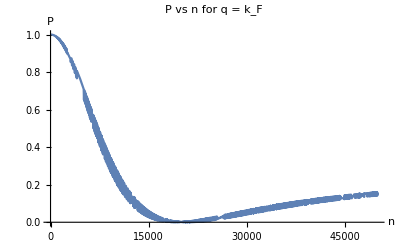

```mathematica
Plot[PO,{n,1,50000}, AxesLabel->{"n", "P"}, PlotLabel->"P vs n for q = k_F"]
```

```mathematica
Clear[n]
```